# Residue Calculus

As a reminder the residue theorem says
	∫_Γ f(z)dz=2π ⅈ   ∑_(j=1)^m w(c_j) r_j
for an analytic function f(z) with singularities at c_1,c_2,…,c_m in Γ. The residues are  r_j=lim_(z→c_j) (z-c_j)f(z) and w is the winding number.
	https://en.wikipedia.org/wiki/Residue_theorem
Chapter 5 is about the techniques that use the residue theorem to compute useful things.

## Contours and Winding Numbers.

The winding number for a contour Γ and a point z_0 is simply how many times the contour goes round the singularity: positive is CCW and negative is CW.  There is a recipe
	1/(2π ⅈ)∫_Γ 1/(z-z_0)dz

```mathematica
p[t_]:= (E^(ⅈ 4π t)+ E^(ⅈ 2π t))
z0=-0.2+0.1I;
w=1/(2π ⅈ)NIntegrate[p'[t]/(p[t]-z0),{t,0,1}];
CurvePic=ParametricPlot[ReIm[p[t]],{t,0,1},
Prolog->{Red, PointSize[0.02],Point[ReIm[sing]]},
PlotLabel->w];
Manipulate[Show[CurvePic,Epilog->{PointSize[0.02],Point[ReIm[p[t]]]}],
{t,0,1}]
```

## Computing Residues

The residue of f(z) at a singularity z_0 is 
	Res(f,z_0)=lim_(z→z_0) (z-z_0)f(z)
A) If f(z)=N(z)/D(z) and D has a simple root at z=z_0 and N(z_0)≠0 then
	Res(f,z_0)=N(z_0)/D'(z_0)
why:	 Res(f,z_0)=lim_(z->z_0) ((z-z_0)N(z))/(D(z))=lim_(z->z_0) (d/dz( 
 (z-z_0)N(z)))/(D'(z))=lim_(z->z_0) ((z-z_0)N'(z) + N(z))/(D'(z))=(N(z_0))/(D(z_0))
B) If f(z) = ϕ(z)/(z - z_0)^m and ϕ(z_0)≠0 then
	Res(f,z_0)=ϕ^(m-1)(z_0)/(m-1)!
why:	 Expand ϕ(z)=∑_(k=0)^∞ (z-z_0)^k(ϕ^k(z_0))/(k!) then
(ϕ(z))/(z-z_0)^m | = | (∑_(k=0)^∞ (z-z_0)^k(ϕ^k(z_0))/(k!))/(z-z_0)^m                                                                                                             
  | = | ∑_(k=0)^∞ (z-z_0)^(k-m)(ϕ^k(z_0))/(k!)                                                                                              
  | = | (ϕ(z_0))/(z-z_0)^m+(ϕ'(z_0))/(1!(z-z_0)^(m-1))+…+(ϕ^(m-1)(z_0))/((m-1)!(z-z_0)^1)+∑_(k=m)^∞ (z-z_0)^(k-m)(ϕ^k(z_0))/(k!)
C) If ϕ(z) has a pole of order m then 
	Res(f,z_0)=1/((m-1)!)lim_(z-z_0) d^(m-1)/dz^(m-1)[ 
 (z-z_0)^m f(z) |  ]
why:	 Expand f(z)=(a_-1)/(z-z_0)^1+∑_(k=2)^m (a_-k)/(z-z_0)^k+∑_(k=0)^∞ (a_k(z-z_0))^k then 
(z-z_0)^m f(z) |   | = | a_-1 (z-z_0)^(m-1)+∑_(k=2)^m a_-k (z-z_0)^(m-k)+∑_(k=0)^∞ (a_k(z-z_0))^(m+k)
  | = | ∑_(k=0)^(m-2) b_k (z-z_0)^k+b_(m-1)(z-z_0)^(m-1)+∑_(k=m)^∞ b_k (z-z_0)^k
where b_k=g^(k)(z_0)/k! and g(z)=(z-z_0)^m f(z).  Matching the boxed terms gives
	a_-1=g^(m-1)(z_0)/(m-1)!

Lets practice some of these and check we are understanding.

## Simple Pole Integrals

#### ∫_Γ ⅇ^z/((1+4 z^2)(z-ⅈ))dz Γ CCW circle of radius 2 around 0

```mathematica
p[t_]:=2 E^(2π ⅈ t)
f[z_]:=ⅇ^z/((1+4 z^2)(z-ⅈ))
FunctionPoles[f[z],z];
{Residue[f[z],{z,ⅈ}],Residue[f[z],{z,ⅈ/2}],Residue[f[z],{z,-ⅈ/2}]}
TabView[{
"3D"->Show[
ComplexPlot3D[f[z],{z,2}],
ParametricPlot3D[{Re[p[t]],Im[p[t]],h},{t,0,1},{h,-1,0.3},PlotPoints->40,Mesh->False,PlotStyle->{Opacity[0.8],LightCyan}]],
"2D"->Show[
ComplexPlot[f[z],{z,2}],
ParametricPlot[ReIm[p[t]],{t,0,1},PlotStyle->Cyan]
]
}]
```

{-ⅇ^ⅈ/3,ⅇ^(ⅈ/2)/2,-1/6 ⅇ^(-ⅈ/2)}

12

#### ∫_Γ ⅇ^z/((1-4 z^2)(z-ⅈ)) Γ the fancy contour below

#### p[t_]:=E^(2π ⅈ t)+2 E^(4π ⅈ t) -0.5ⅈ f[z_]:=ⅇ^z/((1-4 z^2)(z-ⅈ)) sings=FunctionPoles[f[z],z]; r1=Residue[f[z],{z, -1/2}]; r2=Residue[f[z],{z, I}]; r3=Residue[f[z],{z, 1/2}]; ans = 2 π ⅈ (2(r1+r3)+r2 ) {NIntegrate[f[p[t]]*p'[t],{t, 0, 1}],N[ans]} Show[ ComplexPlot[f[z],{z,4}], ParametricPlot[ReIm[p[t]],{t,0,1},PlotStyle->Cyan], Epilog->Point[ReIm[sings⟦All,1⟧]]]

2 ⅈ (2 (-(1/10-ⅈ/5)/(√ⅇ)-(1/10+ⅈ/5) √ⅇ)+ⅇ^ⅈ/5) π

{1.56189-2.15507 ⅈ,1.56189-2.15507 ⅈ}

-Graphics-

## Essential Singularity Example

#### ∫_Γ (z^3+a)ⅇ^(1/z)dz Γ CCW circle of radius 2 around 1

f has an essential singularity at z=0.  Substituting u=1/z in the TS ⅇ^u=∑_(k=0)^∞ u^k/(k!) gives the Laurent series
	(z^3+a)ⅇ^(1/z)=(z^3+a)∑_(k=0)^∞ 1/(z^k k!)=z^3+z^2+z/2+(a+1/6)+(1/24+a)/z+…	
 so the residue at z=0 is r=a+1/24.  The singularity is inside the contour so we should get
 	∫_Γ (z^3+a)ⅇ^(1/z)dz=2π ⅈ (a+1/24)

{2.13163×10^-14+19.1114 ⅈ,0.+19.1114 ⅈ}

-Graphics3D-

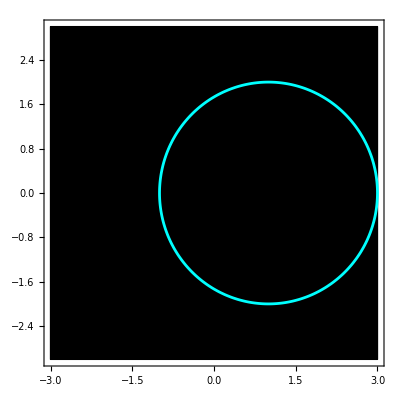

```mathematica
p[t_]:=1+2 E^(2π ⅈ t)
a=3.0;
f[z_]:=(z^3+a)ⅇ^(1/z)
{NIntegrate[f[p[t]]p'[t],{t,0,1}],2π ⅈ (a + 1/24)}
ComplexPlot3D[f[z],{z,3},PlotLegends->Automatic]
Show[
ComplexPlot[f[z],{z,3},PlotLegends->Automatic],
ParametricPlot[ReIm[p[t]],{t,0,1},PlotStyle->Cyan]
]
```

## Real Axis Integral Examples

#### ∫_(-∞)^∞ x^2/(1+x^4)dx: Ex 5.4 on p122

f(z) has 4 simple poles at 
	z=±1/(√2)(1±ⅈ) 
or if you prefer
	z=ⅇ^(ⅈ (π/4 + k π/2)) for k=0,1,2,3.
Consider the CCW contour Γ_R that goes along the real axis from R  to -R and round the semicircle radius R  in the lower half plane.  If R>1 then the two poles in the lower half plane
	z_3=1/(√2)(1-ⅈ)  and  z_4=1/(√2)(-1-ⅈ)
are inside the contour.  For R>1 the contour integral is independent of R and
	∫_Γ_R f(z)dz=2π ⅈ (Res(f,z_3)+Res(f,z_4))=2π ⅈ (-ⅈ/(2 √2))=-π/(√2)
So for R>1 
	∫_0^1 f(p_1(t)) p_1'(t)dt+∫_0^1 f(p_2(t)) p_2'(t)dt=-π/(√2) 
where 
	p_1(t)=R-2R t  and p_2(t)=R ⅇ^(ⅈ (π + π t)).
We have 
	|∫_0^1 f(p_2(t)) p_2'(t)dt |≤∫_0^1|f(p_2(t))| | p_2'(t)|dt 
with 
	| p_2'(t)|=| ⅈ π R ⅇ^(ⅈ (π + π t))|=π R 
and 
	 |f(p_2(t))|=|((R ⅇ^(ⅈ (π + π t)))^2)/(1 + (R ⅇ^(ⅈ (π + π t)))^4) |=|(R^2  ⅇ^(2ⅈ (π + π t)))/(1 +R^4 ⅇ^(4ⅈ (π + π t))) |
so as R→∞
	|f(p_2(t))|=(|R^2  ⅇ^(2ⅈ (π + π t))|)/(|1 +R^4 ⅇ^(4ⅈ (π + π t))|) =R^2/(|1 +R^4 ⅇ^(4ⅈ (π + π t))|) ≈ R^2/R^4=1/R^2.
Assembling these estimates we get as R→∞
	|∫_0^1 f(p_2(t)) p_2'(t)dt |≈∫_0^1 (π R)/R^2 dt=π/R→0.
Since p_1(0)=R and p_1(1)=-R the calculus II substitution x=p_1(t) and dx=p_1'(t) shows that 
	∫_R^-R f(x)dx=∫_0^1 f(p_1(t)) p_1'(t)dt.

Finally if we let R->∞ in  
	∫_R^-R f(x) dx+∫_0^1 f(p_2(t)) p_2'(t)dt=-π/(√2)
and remember that ∫_0^1 f(p_2(t)) p_2'(t)dt⟶0  we get
	∫_∞^(-∞) f(x) dx=lim_(R→∞) ∫_R^-R f(x) dx=-π/(√2)
This time it is the end flipping the limits of integration gives
	∫_(-∞)^∞ f(x) dx=π/(√2)

-ⅈ √2

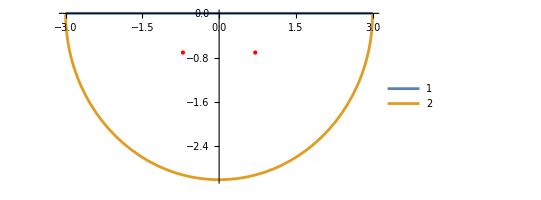

```mathematica
f[z_]:=z^2/(1+z^4)
{z3,z4}={1/(√2)(1-ⅈ),1/(√2)(-1-ⅈ)};
z3+z4
{r3,r4}=Map[Residue[f[z],{z,#}]&,{z3,z4}];
P1[R_][t_]:=R-2R t
P2[R_][t_]:=R ⅇ^(ⅈ (π + π t))
R=3;
ParametricPlot[{ReIm[P1[R][t]],ReIm[P2[R][t]]},
{t,0,1},PlotLegends->Automatic,
Epilog->{Red,Point[ReIm[{z3,z4}]]}]
```

Notes: 
A) Closing the contour in the top half plane just gives different minus signs to deal with!
B) Mathematica can compute an antiderivative and the integral.

```mathematica
{Integrate[x^2/(1+x^4),{x,-∞,∞}],Integrate[x^2/(1+x^4),x]}
```

{π/(√2),(-2 ArcTan[1-√2 x]+2 ArcTan[1+√2 x]+Log[1-√2 x+x^2]-Log[1+√2 x+x^2])/(4 √2)}

#### ∫_(-∞)^∞ (cos(k x))/((x+b)^2+a^2)dx: Ex 5.5 on p124

The simplest way to deal with the cos(k x) is to compute
	∫_(-∞)^∞ (exp(ⅈ k x))/((x+b)^2+a^2)dx=∫_(-∞)^∞ (cos(k x))/((x+b)^2+a^2)dx+ⅈ∫_(-∞)^∞ (sin(k x))/((x+b)^2+a^2)
and take the real part. The function
	f(z)=(exp(ⅈ k z))/((z+b)^2+a^2) 
has 2 simple poles at 
	z_1=-b- a ⅈ  and z_2=-b+a ⅈ 
The residues are straight forward to compute since  
	f(z)=(exp(ⅈ k z))/((z+b)^2+a^2)=(exp(ⅈ k z))/((z + b + a ⅈ)(z + b - a ⅈ))=(exp(ⅈ k z))/((z -z_1)(z -z_2))
we get
	r_1=(exp(ⅈ k z_1))/(z_1-z_2)=-(ⅈ ⅇ^(-(a+ⅈ b) k))/(2 a) 
and
	r_2=(exp(ⅈ k z_2))/(z_2-z_1)=(ⅈ ⅇ^((a-ⅈ b) k))/(2 a) 
Provided k>0 
	|f(x+ⅈ y)|=ⅇ^(-k y)/((|(x+b)+ ⅈ y))^2+a^2|)=ⅇ^(-k y)/(|((x+b)^2-y^2 + a^2)+2 ⅈ (x+b)y|)
so 
	|f(x+ⅈ y)|=ⅇ^(-k y)/(√(((x+b)^2-y^2 + a^2)^2+(2(x+b)y)^2))≈ⅇ^(-k y)/(√((x^2-y^2)^2+ (2x y)^2))=ⅇ^(-k y)/(√((x^2+y^2)^2))=ⅇ^(-k y)/(x^2+y^2).

```mathematica
f[a_,b_,k_][z_]:=Exp[ⅈ k z]/((z+b)^2+a^2)
{z1,z2}={-b+ⅈ a, -b - ⅈ a};
{r1,r2}=Map[Residue[f[a,b,k][z],{z,#}]&,{z1,z2}]
ComplexPlot3D[f[1,0.3,0.8][z],{z,4},
AxesLabel->{"re","im"}]
```

{-(ⅈ ⅇ^(-((a+ⅈ b) k)))/(2 a),(ⅈ ⅇ^((a-ⅈ b) k))/(2 a)}

-Graphics3D-

As |z| gets big |f(z)|≈ⅇ^(-k y)/(|z|^2) which gets small in the upper half plane! Close the contour with a semi-circle of radius R in the upper half plane.   If R>√(a^2+b^2) then only the pole at z_1=-a+b ⅈ is inside the contour and
	∫_0^1 f(p_1(t))p_1'(t)dt+∫_0^1 f(p_2(t))p_2'(t)dt=2π ⅈ r_1=(ⅇ^(-((a+ⅈ b) k)) π)/a
The first integral is our target so
	∫_-R^R f(x)dx+∫_0^1 f(p_2(t))p_2'(t)dt=(ⅇ^(-((a+ⅈ b) k)) π)/a.
The second integral satisfies
	|∫_0^1 f(p_2(t))p_2'(t)dt|≤∫_0^1|f(R ⅇ^(ⅈ π t))R ⅈ π ⅇ^(ⅈ π t)|dt≈π/R∫_0^1 ⅇ^(-k R sin(π t))dt|≤π/R   
so the second integral goes to zero as R→∞. Taking the limits gives us 
	∫_(-∞)^∞ f(x)dx=(ⅇ^(-((a+ⅈ b) k)) π)/a
We want the real part of this is our original target so
	∫_(-∞)^∞ (cos(k x))/((x+b)^2+a^2)dx=Re[∫_(-∞)^∞ (exp(ⅈ k x))/((x+b)^2+a^2)dx]=Re[(ⅇ^(-((a+ⅈ b) k)) π)/a]=(ⅇ^(-a k) π Cos[b k])/a.

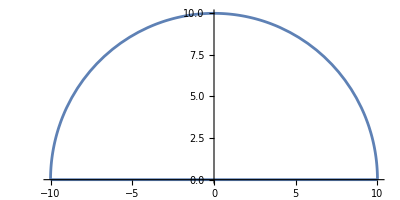

$Aborted

```mathematica
p1[R_][t_]:=-R+2R t
p2[R_][t_]:=R ⅇ^(ⅈ π t)
R=10;
ParametricPlot[ReIm[{p1[R][t],p2[R][t]}],{t,0,1}]
```

#### ∫_0^(2π) 1/(A+sin(θ))dθ: Ex 5.7 on p126 Method 1

This is a bit different.  Lets assume A>1 so there are no singularities on the real line!

```mathematica
Clear[f]
f[A_][z_]:=1/(A+Sin[z])
TabView[{
"re"->Plot[ f[1.2][x],{x,0,4π}],
"comp 3D"->ComplexPlot3D[f[1.2][z],{z,4π},
PlotRange->{0, 6},
PlotLegends->Automatic,
AxesLabel->{"re","im","abs"}],
"comp 2D"->ComplexPlot[f[1.2][z],{z,4π},
PlotLegends->Automatic,
AxesLabel->{"re","im"}]
}]
```

123

We need to choose a contour where one piece gives us the integral we want and the sum of the other pieces are easily evaluated in some way.  The key is the periodicity in the real direction and the exponential growth of sin(x+ⅈ y) as y→∞.   The rectangle contour in ℂ parameterized below will work.

```mathematica
p1[L_][t_]:=0 + 2π t
p2[L_][t_]:=2π + ⅈ L t
p3[L_][t_]:=ⅈ L +2π (1-t)
p4[L_][t_]:=ⅈ L(1-t)
L=10;
Show[
ComplexPlot[f[1.2][z],{z,0.0,2π + L ⅈ}],
ParametricPlot[
Evaluate[ReIm[{p1[L][t],p2[L][t],p3[L][t],p4[L][t]}]],{t,0,1},
PlotLegends->Automatic
]
]
```

-Graphics-

Notes: 
The bottom∫_Γ_1 f(z)dx is the bite we want.
The vertical sides satisfy ∫_Γ_2 f(z)dx=-∫_Γ_4 f(z)dx because of periodicity.
The top ∫_Γ_3 f(z)dx→0 as L→∞. 
A single singularity (where A+sin(z)=0) is visible inside the contour.  There is a simple pole at
	z_1=-ArcSin[A].
It is complex because A>1. We might need to pick the correct branch of ArcSin!

```mathematica
A=1.2;
TabView[{
"3D"->ComplexPlot3D[f[A][z],{z,0.0,2π + 2 ⅈ},
PlotRange->{0,10},
PlotLabel->StringForm["A=``",A]],
"z_1(A)"->Plot[{Re[-ArcSin[A]],Im[-ArcSin[A]]},{A,1,100},
PlotLegends->{"re","im"},
AxesLabel->{"A",None},
GridLines->Automatic]
}]
```

12

Lets see if the software can evaluate the residue.

```mathematica
Residue[f[A][z],{z,-ArcSin[A]}]
```

1/(√(1-A^2))

Lets see if we can work out how it did that!

```mathematica
Clear[A]
z1=-ArcSin[A]
Num[z_]:=1
Den[z_]:=A + Sin[z]
{Den'[z],Den'[z1]}
```

-ArcSin[A]

{Cos[z],√(1-A^2)}

Assembling all this and taking L→∞ we have
	∫_0^(2π) 1/(A+sin(θ))dθ=(2π)/(√(A^2-1))
Checking a particular value!

```mathematica
A=1.2;
{NIntegrate[1/(A+Sin[θ]),{θ,0,2π}],(2π)/(√(A^2-1))}
```

{9.47226,9.47226}